```mathematica
f[n_, c_, s_] := c^-2 Sum[ j^-s k^-s,{j,2,c^2 n},{k,2,c^2 n /j }]-2 c^-2  Sum[ j^-s k^-s,{j,2,c},{k,2,c^2 n /j }] + c^-2  Sum[ j^-s k^-s,{j,2,c},{k,2,c }]
```

```mathematica
f[6,1,aa=-1]-f[5,1,aa]
```

12

```mathematica
d2[n_,k_,s_]:=Sum[j^-s d2[n/j,k-1,s],{j,2,n}];d2[n_,0,s_]:=1
```

```mathematica
N[d2[30,2,-1]]
```

1020.

```mathematica
N[f[30,20,-1]]
```

513682.

```mathematica
N[Gamma[2,0,-Log[100]]/Gamma[2]]
```

361.517-4.41506×10^-14 ⅈ

```mathematica
N[Gamma[2,0,-(1-(-1))Log[30]]/Gamma[2]]
N[Gamma[2,0,-Log[30]]/Gamma[2]]
N[Gamma[2,0,-(1-ZetaZero[1])Log[30]]/Gamma[2]]
```

5223.16-6.3953×10^-13 ⅈ

73.0359-8.82186×10^-15 ⅈ

213.126+156.055 ⅈ

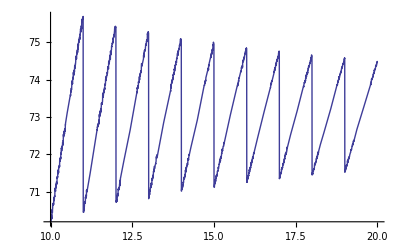

```mathematica
Plot[f[30,c,0],{c,10,20}]
```

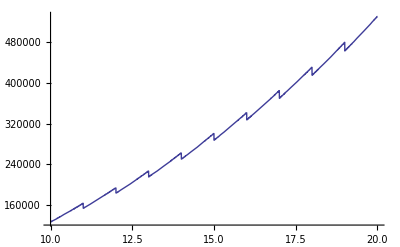

```mathematica
Plot[f[30,c,-1],{c,10,20}]
```

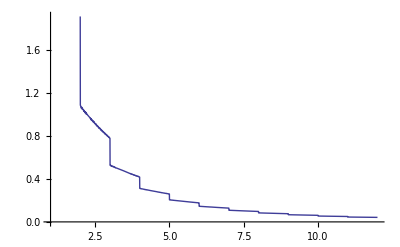

```mathematica
Plot[f[30,c,1],{c,1,12}]
```

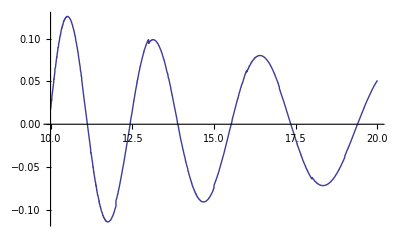

```mathematica
Plot[Re[f[30,c,N[ZetaZero[1]]]],{c,10,20}]
```

```mathematica
N[dc[30,2,20,-1]]
```

513682.

```mathematica
d2[30,2,-1]
```

1020

```mathematica
f[30,14,-1]
```

48925223/196

```mathematica
N[Gamma[2,0,-(1-(-1))Log[30]]/Gamma[2]]
```

5223.16-6.3953×10^-13 ⅈ

```mathematica
dc[n_, k_, c_, s_] := Sum[ (j)^-s c^(-1) dc[c n / j, k-1, c, s],{j,1+c, n c^k}];dc[n_, 0,c_,s_]:=1
```

```mathematica
N[dc[30,2,1,-1]]
```

1020.

```mathematica
Sum[ j,{j,2,30}]
```

464